```mathematica
Trials for Good equation rescaling
This notebook is for comparing the good equation rescaling to the Ugly one, doing the same but only having different differential equation
```

equation for Good rescaling Trials

```mathematica
ClearAll["Global`*"]
```

## Compute geometric quantities

In this section we define the coordinates, metric, Christoffels and curvature. This is just geometry-- all in spherical polar coords.

Define coordinates

```mathematica
X={T,R,θ,ϕ};
```

Define 4-metric

```mathematica
g={{-1,0,0,0},{0,1,0,0},{0,0,R^2,0},{0,0,0,R^2 Sin[θ]^2}};g//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[θ]^2)

```mathematica
ginv=g//Inverse//Simplify;ginv//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/R^2 | 0
0 | 0 | 0 | Csc[θ]^2/R^2)

Compute Christoffels:

(Γ^γ)_αβ = 1/2 g^γζ(g_(αζ,β)+g_(ζβ,α)-g_(αβ,ζ))

```mathematica
Christoffelsudd = Table[1/2 Sum[ginv[[γ,ζ]](D[g[[ζ,β]], X[[α]]]+D[g[[α,ζ]], X[[β]]]-D[g[[α,β]], X[[ζ]]]),{ζ,4}],{γ,4},{α,4},{β,4}]//Simplify;
```

```mathematica
Table[Table[Christoffelsudd[[γ,α,β]],{γ,4}],{α,4},{β,4}]//MatrixForm
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
1/R
0) | (0
0
0
1/R)
(0
0
0
0) | (0
0
1/R
0) | (0
-R
0
0) | (0
0
0
Cot[θ])
(0
0
0
0) | (0
0
0
1/R) | (0
0
0
Cot[θ]) | (0
-R Sin[θ]^2
-Cos[θ] Sin[θ]
0))

Define Contracted Christoffels

Γ^a = g^μν (Γ^a)_μν ; Γ_a = g_ab Γ^b

```mathematica
ContractedChristoffelsu=Table[Sum[ginv[[a,b]]Christoffelsudd[[c,a,b]],{a,4},{b,4}],{c,4}]//Simplify
```

{0,-2/R,-Cot[θ]/R^2,0}

```mathematica
ContractedChristoffelsd=Table[Sum[g[[a,b]]ContractedChristoffelsu[[b]],{b,4}],{a,4}]//Simplify
```

{0,-2/R,-Cot[θ],0}

Riemann Christoffel Tensor:

(R^μ)_ναβ = ∂_α (Γ^μ)_νβ -  ∂_β (Γ^μ)_αν + (Γ^μ)_αζ (Γ^ζ)_νβ - (Γ^μ)_βζ (Γ^ζ)_αν

```mathematica
Reimuddd=Table[D[Christoffelsudd[[μ,ν,β]], X[[α]]]-D[Christoffelsudd[[μ,α,ν]], X[[β]]]+Sum[Christoffelsudd[[μ,α,ζ]]Christoffelsudd[[ζ,ν,β]],{ζ,4}]-Sum[Christoffelsudd[[μ,β,ζ]]Christoffelsudd[[ζ,α,ν]],{ζ,4}],{μ,4},{ν,4},{α,4},{β,4}]//Simplify;Reimuddd//MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

Ricci Tensor

R_μν= (R^α)_μαν

```mathematica
Riccidd=Table[Sum[Reimuddd[[α,μ,α,ν]],{α,4}],{μ,4},{ν,4}]//Simplify;Riccidd//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Ricci Scalar

R = (R^μ)_μ= g^μν R_μν

```mathematica
Ricci=Sum[ginv[[μ,ν]]Riccidd[[μ,ν]],{μ,4},{ν,4}]//Simplify
```

0

## Setup Good wave Equation:

Setup the Good Scalar Wave Equation:

□ψ = 0

```mathematica
BoxPsi=Sum[ginv[[a,b]]D[ψ[T,R], X[[a]],X[[b]]],{a,4},{b,4}]-Sum[ContractedChristoffelsu[[c]]D[ψ[T,R], X[[c]]],{c,4}]//Simplify
```

(2 ψ^(0,1)[T,R])/R+ψ^(0,2)[T,R]-ψ^(2,0)[T,R]

```mathematica
ContractedCovDerivative = Sum[ginv[[a,b]]D[ψ[T,R], X[[b]]]D[ψ[T,R], X[[a]]],{a,4},{b,4}]//Simplify
```

(ψ^(0,1)[T,R])^2-(ψ^(1,0)[T,R])^2

```mathematica
Model1=BoxPsi+ContractedCovDerivative==0
```

(2 ψ^(0,1)[T,R])/R+(ψ^(0,1)[T,R])^2+ψ^(0,2)[T,R]-(ψ^(1,0)[T,R])^2-ψ^(2,0)[T,R]==0

```mathematica
DynamicalScalarWaveRule=Solve[Model1,{D[ψ[T,R], T,T]}]//Flatten//FullSimplify
```

{ψ^(2,0)[T,R]→(2 ψ^(0,1)[T,R])/R+(ψ^(0,1)[T,R])^2+ψ^(0,2)[T,R]-(ψ^(1,0)[T,R])^2}

First order reduced scalar fields:

ψ_+ =  ∂_T ψ + ∂_R ψ; ψ_- = ∂_T ψ - ∂_R ψ .

```mathematica
PsiPlusMinusDefinition={PsiPlus=SubPlus[ψ][T,R]==D[ψ[T,R], T]+D[ψ[T,R], R],PsiMinus=SubMinus[ψ][T,R]==D[ψ[T,R], T]-D[ψ[T,R], R]}
```

{ψ_+[T,R]==ψ^(0,1)[T,R]+ψ^(1,0)[T,R],ψ_-[T,R]==-ψ^(0,1)[T,R]+ψ^(1,0)[T,R]}

```mathematica
DerPsiRules=Solve[PsiPlusMinusDefinition,{D[ψ[T,R], X[[1]]],D[ψ[T,R], X[[2]]]}]//Flatten
```

{ψ^(1,0)[T,R]→1/2 (ψ_-[T,R]+ψ_+[T,R]),ψ^(0,1)[T,R]→1/2 (-ψ_-[T,R]+ψ_+[T,R])}

```mathematica
InverseDerPsiRules=PsiPlusMinusDefinition/.Equal->Rule
```

{ψ_+[T,R]→ψ^(0,1)[T,R]+ψ^(1,0)[T,R],ψ_-[T,R]→-ψ^(0,1)[T,R]+ψ^(1,0)[T,R]}

```mathematica
PsiPlusMinusDot=D[PsiPlusMinusDefinition, X[[1]]]//Simplify
```

{(ψ_+)^(1,0)[T,R]==ψ^(1,1)[T,R]+ψ^(2,0)[T,R],(ψ_-)^(1,0)[T,R]+ψ^(1,1)[T,R]==ψ^(2,0)[T,R]}

```mathematica
PsiDoubleDotRule={Solve[PsiPlusMinusDot[[1]],Derivative[2,0][ψ][T,R]],Solve[PsiPlusMinusDot[[2]],Derivative[2,0][ψ][T,R]]}//Flatten
```

{ψ^(2,0)[T,R]→(ψ_+)^(1,0)[T,R]-ψ^(1,1)[T,R],ψ^(2,0)[T,R]→(ψ_-)^(1,0)[T,R]+ψ^(1,1)[T,R]}

```mathematica
PsiPlusMinusDash=D[PsiPlusMinusDefinition, X[[2]]]//Simplify
```

{(ψ_+)^(0,1)[T,R]==ψ^(0,2)[T,R]+ψ^(1,1)[T,R],(ψ_-)^(0,1)[T,R]+ψ^(0,2)[T,R]==ψ^(1,1)[T,R]}

```mathematica
PsiDoubleDerRules=Solve[PsiPlusMinusDash,{Derivative[1,1][ψ][T,R],Derivative[0,2][ψ][T,R]}]//Simplify//Flatten
```

{ψ^(1,1)[T,R]→1/2 ((ψ_-)^(0,1)[T,R]+(ψ_+)^(0,1)[T,R]),ψ^(0,2)[T,R]→1/2 (-(ψ_-)^(0,1)[T,R]+(ψ_+)^(0,1)[T,R])}

Substitute in the model 1 equation

```mathematica
DerPsiRules[[1]]/.Rule->Equal
```

ψ^(1,0)[T,R]==1/2 (ψ_-[T,R]+ψ_+[T,R])

```mathematica
PsiPlusEvolutionRule=Solve[Model1/.PsiDoubleDotRule[[1]]/.PsiDoubleDerRules/.DerPsiRules,Derivative[1,0][SubPlus[ψ]][T,R]]//Simplify//Flatten
```

{(ψ_+)^(1,0)[T,R]→(ψ_+[T,R]-ψ_-[T,R] (1+R ψ_+[T,R])+R (ψ_+)^(0,1)[T,R])/R}

```mathematica
PsiMinusEvolutionRule=Solve[Model1/.PsiDoubleDotRule[[2]]/.PsiDoubleDerRules/.DerPsiRules,Derivative[1,0][SubMinus[ψ]][T,R]]//Simplify//Flatten
```

{(ψ_-)^(1,0)[T,R]→(ψ_+[T,R]-ψ_-[T,R] (1+R ψ_+[T,R])-R (ψ_-)^(0,1)[T,R])/R}

```mathematica
PsiZeroPlusMinusEvolutionRules={DerPsiRules[[1]],PsiPlusEvolutionRule,PsiMinusEvolutionRule}//Flatten
```

{ψ^(1,0)[T,R]→1/2 (ψ_-[T,R]+ψ_+[T,R]),(ψ_+)^(1,0)[T,R]→(ψ_+[T,R]-ψ_-[T,R] (1+R ψ_+[T,R])+R (ψ_+)^(0,1)[T,R])/R,(ψ_-)^(1,0)[T,R]→(ψ_+[T,R]-ψ_-[T,R] (1+R ψ_+[T,R])-R (ψ_-)^(0,1)[T,R])/R}

We now rewrite some terms using the Evans method: the PsiPlus term becomes:

```mathematica
/.(SubPlus[ψ][T,R]-SubMinus[ψ][T,R] (1+R SubPlus[ψ][T,R])+R Derivative[0,1][SubPlus[ψ]][T,R])/R->1/2((2 SubPlus[ψ][T,R])/R+ Derivative[0,1][SubPlus[ψ]][T,R])-1/2((2 SubMinus[ψ][T,R])/R+Derivative[0,1][SubMinus[ψ]][T,R])-SubMinus[ψ][T,R] SubPlus[ψ][T,R]+ 1/2 Derivative[0,1][SubPlus[ψ]][T,R]+ 1/2 Derivative[0,1][SubMinus[ψ]][T,R]
```

And the PsiMinus:

```mathematica
/.(SubPlus[ψ][T,R]-SubMinus[ψ][T,R] (1+R SubPlus[ψ][T,R])-R Derivative[0,1][SubMinus[ψ]][T,R])/R->1/2((2 SubPlus[ψ][T,R])/R+ Derivative[0,1][SubPlus[ψ]][T,R])-1/2((2 SubMinus[ψ][T,R])/R+Derivative[0,1][SubMinus[ψ]][T,R])-SubMinus[ψ][T,R] SubPlus[ψ][T,R]- 1/2 Derivative[0,1][SubPlus[ψ]][T,R]- 1/2 Derivative[0,1][SubMinus[ψ]][T,R]
```

```mathematica
PsiZeroPlusMinusEvolutionEquations=PsiZeroPlusMinusEvolutionRules/.Rule->Equal;
```

```mathematica
PsiConstraint=DerPsiRules[[2]]/.Rule->Equal
```

ψ^(0,1)[T,R]==1/2 (-ψ_-[T,R]+ψ_+[T,R])

## Introduce first trial of Rescalings:

Good Rescaling:

ψ  -->  Rψ ; ψ_+ --> (R.b2ψ)_+ ; ψ_- --> Rψ_-. Afterwards, for the origin to work, we’ll have to take χ ~ R instead of R.

```mathematica
FirstGoodRescaling={ψ->Function[{T,R},Rψ[T,R]/χ[R]],SubPlus[ψ]->Function[{T,R},SubPlus[R.b2ψ][T,R]/χ[R]^2],SubMinus[ψ]->Function[{T,R},SubMinus[Rψ][T,R]/χ[R]]}
```

{ψ→Function[{T,R},Rψ[T,R]/χ[R]],ψ_+→Function[{T,R},((R.b2ψ)_+[T,R])/χ[R]^2],ψ_-→Function[{T,R},(Rψ_-[T,R])/χ[R]]}

```mathematica
(*SecondUglyRescaling=R2ψ_+[T,R]->R3ψ_+[T,R]/χ[R];*)
```

```mathematica
FirstGoodRescaledEquations=Solve[PsiZeroPlusMinusEvolutionRules/.FirstGoodRescaling/.Rule->Equal//Simplify,{Derivative[1,0][Rψ][T,R],Derivative[1,0][SubPlus[R.b2ψ]][T,R],Derivative[1,0][SubMinus[Rψ]][T,R]}]//Flatten//Simplify
```

{Rψ^(1,0)[T,R]→(χ[R] Rψ_-[T,R]+(R.b2ψ)_+[T,R])/(2 χ[R]),((R.b2ψ)_+)^(1,0)[T,R]→-(χ[R] Rψ_-[T,R])/R+((R.b2ψ)_+[T,R])/R-((R.b2ψ)_+[T,R] (Rψ_-[T,R]+2 χ'[R]))/χ[R]+((R.b2ψ)_+)^(0,1)[T,R],(Rψ_-)^(1,0)[T,R]→(-R Rψ_-[T,R] (R.b2ψ)_+[T,R]+χ[R] ((R.b2ψ)_+[T,R]+R Rψ_-[T,R] χ'[R])-χ[R]^2 (Rψ_-[T,R]+R (Rψ_-)^(0,1)[T,R]))/(R χ[R]^2)}

## Change of Coordinates:

Change of Coordinate Rules:

{T,R} --> {t,r}

```mathematica
(*change of coordinates*)
coorsubs={T->Tf[t,r],R->Rf[r]}
```

{T→Tf[t,r],R→Rf[r]}

```mathematica
(*coordinate systems*)
Xcoor={T,R};x={t,r};
```

```mathematica
(*corresponding Jacobian (dX/dx) and its inverse (dx/dX)*)
(Jac=Table[D[Xcoor[[c2]]/.coorsubs,x[[c1]]],{c1,1,Length@x},{c2,1,Length@Xcoor}])//MatrixForm (*{{D[Texpr,t],D[Texpr,r]},{D[Rexpr,t],D[Rexpr,r]}}*)
(*Here, rows vary with c1, or x, and columns with c2, i.e. X.*)
(InvJac=Inverse@Jac)//MatrixForm(*Here, rows vary with X and columns with x.*)
Jac.InvJac//MatrixForm
```

(Tf^(1,0)[t,r] | 0
Tf^(0,1)[t,r] | Rf'[r])

(1/(Tf^(1,0)[t,r]) | 0
-(Tf^(0,1)[t,r])/(Rf'[r] Tf^(1,0)[t,r]) | 1/Rf'[r])

(1 | 0
0 | 1)

```mathematica
(*rule for changing the derivatives - I am assuming that only first derivatives of T and R appear*)
derchange={Table[D[zz_[T,R],Xcoor[[count]]]->Sum[InvJac[[count,sum]]D[zz[t,r],x[[sum]]],{sum,1,Length@x}],{count,1,Length@Xcoor}](*,D[zz_[R],Xcoor[[2]]]->InvJac[[2,2]]D[zz[r],x[[2]]]*)}//Flatten
```

{zz_^(1,0)[T,R]→(zz^(1,0)[t,r])/(Tf^(1,0)[t,r]),zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-(Tf^(0,1)[t,r] zz^(1,0)[t,r])/(Rf'[r] Tf^(1,0)[t,r])}

```mathematica
(*rule to change derivatives and function dependence on coordinates, this is the one to use on the equations, together with "coorsubs"*)
changerules={derchange,zz_[T,R]->zz[t,r](*,zz_[R]->zz[Rf[r]]*)}//Flatten
```

{zz_^(1,0)[T,R]→(zz^(1,0)[t,r])/(Tf^(1,0)[t,r]),zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-(Tf^(0,1)[t,r] zz^(1,0)[t,r])/(Rf'[r] Tf^(1,0)[t,r]),zz_[T,R]→zz[t,r]}

Hyperboloidal Coordinates:

T = t + H(R) = t + R(r) - r;
Taking dH/dR = (R’ - 1)/R’
=> H’ = dH/dr = H’ R’ = R’ (R’ - 1)/R’  = R’ - 1
=> H(r) = R(r) - r, demanding that H(0) = 0.

```mathematica
TRule=Tf->Function[{t,r},t+Rf[r]-r]
```

Tf→Function[{t,r},t+Rf[r]-r]

```mathematica
changerules/.TRule
```

{zz_^(1,0)[T,R]→zz^(1,0)[t,r],zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-((-1+Rf'[r]) zz^(1,0)[t,r])/Rf'[r],zz_[T,R]→zz[t,r]}

Redefining all the fields and functions as functions of hyperboloidal coordinates:

Good Rescaled Variables:

```mathematica
GoodRescaledHypGridFunctions=FirstGoodRescaling/.changerules//Flatten
```

{ψ→Function[{t,r},Rψ[t,r]/χ[R]],ψ_+→Function[{t,r},((R.b2ψ)_+[t,r])/χ[R]^2],ψ_-→Function[{t,r},(Rψ_-[t,r])/χ[R]]}

```mathematica
(*∂_T FirstUglyRescaling/.changerules/.TRule*)
```

```mathematica
FirstGoodRescalingHypSlices=FirstGoodRescaling/.changerules/.TRule/.coorsubs
```

{ψ→Function[{t,r},Rψ[t,r]/χ[Rf[r]]],ψ_+→Function[{t,r},((R.b2ψ)_+[t,r])/χ[Rf[r]]^2],ψ_-→Function[{t,r},(Rψ_-[t,r])/χ[Rf[r]]]}

Good Rescaled Equations:

```mathematica
GoodRescaledEquationsHypSlices=Solve[FirstGoodRescaledEquations/.changerules/.TRule/.coorsubs/.Rule->Equal//Simplify,{Derivative[1,0][Rψ][t,r], Derivative[1,0][SubPlus[R.b2ψ]][t,r],Derivative[1,0][SubMinus[Rψ]][t,r]}]//FullSimplify
```

{{Rψ^(1,0)[t,r]→1/2 (Rψ_-[t,r]+((R.b2ψ)_+[t,r])/χ[Rf[r]]),((R.b2ψ)_+)^(1,0)[t,r]→(-Rf'[r] (χ[Rf[r]]^2 Rψ_-[t,r]-χ[Rf[r]] (R.b2ψ)_+[t,r]+Rf[r] (R.b2ψ)_+[t,r] (Rψ_-[t,r]+2 χ'[Rf[r]]))+Rf[r] χ[Rf[r]] ((R.b2ψ)_+)^(0,1)[t,r])/(Rf[r] χ[Rf[r]] (-1+2 Rf'[r])),(Rψ_-)^(1,0)[t,r]→((-χ[Rf[r]] Rψ_-[t,r]+(R.b2ψ)_+[t,r]) Rf'[r])/(Rf[r] χ[Rf[r]])+(Rψ_-[t,r] Rf'[r] (-(R.b2ψ)_+[t,r]+χ[Rf[r]] χ'[Rf[r]]))/χ[Rf[r]]^2-(Rψ_-)^(0,1)[t,r]}}

```mathematica
Collect[GoodRescaledEquationsHypSlices,{SubPlus[R.b2ψ][t,r],SubMinus[Rψ][t,r],Derivative[0,1][SubPlus[R.b2ψ]][t,r], Derivative[0,1][SubMinus[Rψ]][t,r]},Simplify]
```

{{Rψ^(1,0)[t,r]→1/2 Rψ_-[t,r]+((R.b2ψ)_+[t,r])/(2 χ[Rf[r]]),((R.b2ψ)_+)^(1,0)[t,r]→(χ[Rf[r]] Rψ_-[t,r] Rf'[r])/(Rf[r]-2 Rf[r] Rf'[r])+(R.b2ψ)_+[t,r] ((Rψ_-[t,r] Rf'[r])/(χ[Rf[r]]-2 χ[Rf[r]] Rf'[r])+(Rf'[r] (χ[Rf[r]]-2 Rf[r] χ'[Rf[r]]))/(Rf[r] χ[Rf[r]] (-1+2 Rf'[r])))+(((R.b2ψ)_+)^(0,1)[t,r])/(-1+2 Rf'[r]),(Rψ_-)^(1,0)[t,r]→(R.b2ψ)_+[t,r] (Rf'[r]/(Rf[r] χ[Rf[r]])-(Rψ_-[t,r] Rf'[r])/χ[Rf[r]]^2)+Rψ_-[t,r] Rf'[r] (-1/Rf[r]+χ'[Rf[r]]/χ[Rf[r]])-(Rψ_-)^(0,1)[t,r]}}

```mathematica
checkpoint0 = Collect[GoodRescaledEquationsHypSlices/.χ->Function[Rf,Sqrt[1+Rf^2]]/.Rf->Function[r,r/(1-r^2/s^2)],{SubPlus[R.b2ψ][t,r],SubMinus[Rψ][t,r],Rψ[t,r],Derivative[0,1][SubPlus[R.b2ψ]][t,r], Derivative[0,1][SubMinus[Rψ]][t,r]},FullSimplify]/.√(1+r^2/((-1+r^2/s^2)^2))->1/(-r^2+s^2)((r^2-s^2)^2+r^2 s^4)^(1/2)/.(√(1+r^2/((-1+r^2/s^2)^2)))^-1->(1/(-r^2+s^2)((r^2-s^2)^2+r^2 s^4)^(1/2))^-1//FullSimplify
```

{{Rψ^(1,0)[t,r]→1/2 Rψ_-[t,r]+((-r^2+s^2) (R.b2ψ)_+[t,r])/(2 √(r^4+s^4+r^2 s^2 (-2+s^2))),((R.b2ψ)_+)^(1,0)[t,r]→((r^2+s^2) Rψ_-[t,r] (r^4+s^4+r^2 s^2 (-2+s^2)+r s^2 (-r^2+s^2) (R.b2ψ)_+[t,r]))/((r^5-4 r^3 s^2-r s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) (R.b2ψ)_+[t,r]-r (r-s)^2 (r+s)^2 (r^4+s^4+r^2 s^2 (-2+s^2)) ((R.b2ψ)_+)^(0,1)[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))),(Rψ_-)^(1,0)[t,r]→((r^2+s^2) (R.b2ψ)_+[t,r])/(r √(r^4+s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) Rψ_-[t,r] (r^2-s^2-r s^2 (R.b2ψ)_+[t,r]))/(r^5+r s^4+r^3 s^2 (-2+s^2))-(Rψ_-)^(0,1)[t,r]}}

we now rewrite the 1/r terms using the Evans method in order to regularize them:
we isolate the problematic coefficient starting from the equation of the time derivative of PsiPlus
step1: rewriting of the irregular coefficient of PsiMinus

```mathematica
((r^2+s^2) SubMinus[Rψ][t,r] (r^4+s^4+r^2 s^2 (-2+s^2)+r s^2 (-r^2+s^2) SubPlus[R.b2ψ][t,r]))/((r^5-4 r^3 s^2-r s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))->((r^2+s^2) SubMinus[Rψ][t,r] (r^3+r s^2 (-2+s^2)+ s^2 (-r^2+s^2) SubPlus[R.b2ψ][t,r]))/((r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+(s^4(r^2+s^2)((2 SubMinus[Rψ][t,r])/r+Derivative[0,1][SubMinus[Rψ]][t,r]))/(2(r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))-(s^4(r^2+s^2)Derivative[0,1][SubMinus[Rψ]][t,r])/(2(r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))
```

step2: rewriting of the irregular coefficient of PsiPlus
we split the coefficient and we add a derivative in order to obtain an Evans term

```mathematica
((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) SubPlus[R.b2ψ][t,r]-r (r-s)^2 (r+s)^2 (r^4+s^4+r^2 s^2 (-2+s^2)) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))->((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) SubPlus[R.b2ψ][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(s^8((2 SubPlus[R.b2ψ][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ]][t,r]))/(2(r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(s^8 Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(2(r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-((r-s)^2 (r+s)^2 (r^4+s^4+r^2 s^2 (-2+s^2)) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))
```

we can simplify the derivative term with the other already present in the equation

```mathematica
+(s^8 Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(2(r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-((r-s)^2 (r+s)^2 (r^4+s^4+r^2 s^2 (-2+s^2)) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))//FullSimplify
```

((-2 (r^2-s^2)^2+s^8/(r^4+s^4+r^2 s^2 (-2+s^2))) ((R.b2ψ)_+)^(0,1)[t,r])/(2 (r^4-4 r^2 s^2-s^4))

in conclusion:

```mathematica
((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) SubPlus[R.b2ψ][t,r]-r (r-s)^2 (r+s)^2 (r^4+s^4+r^2 s^2 (-2+s^2)) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))->((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) SubPlus[R.b2ψ][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(s^8((2 SubPlus[R.b2ψ][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ]][t,r]))/(2(r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+((-2 (r^2-s^2)^2+s^8/(r^4+s^4+r^2 s^2 (-2+s^2))) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(2 (r^4-4 r^2 s^2-s^4))
```

```mathematica
checkpoint1 = checkpoint0/.((r^2+s^2) SubMinus[Rψ][t,r] (r^4+s^4+r^2 s^2 (-2+s^2)+r s^2 (-r^2+s^2) SubPlus[R.b2ψ][t,r]))/((r^5-4 r^3 s^2-r s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))->((r^2+s^2) SubMinus[Rψ][t,r] (r^3+r s^2 (-2+s^2)+ s^2 (-r^2+s^2) SubPlus[R.b2ψ][t,r]))/((r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+(s^4(r^2+s^2)((2 SubMinus[Rψ][t,r])/r+Derivative[0,1][SubMinus[Rψ]][t,r]))/(2(r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))-(s^4(r^2+s^2)Derivative[0,1][SubMinus[Rψ]][t,r])/(2(r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))/.((r^8-s^8-r^6 s^2 (2+s^2)+r^2 s^6 (2+s^2)) SubPlus[R.b2ψ][t,r]-r (r-s)^2 (r+s)^2 (r^4+s^4+r^2 s^2 (-2+s^2)) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))->((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) SubPlus[R.b2ψ][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(s^8((2 SubPlus[R.b2ψ][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ]][t,r]))/(2(r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+((-2 (r^2-s^2)^2+s^8/(r^4+s^4+r^2 s^2 (-2+s^2))) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(2 (r^4-4 r^2 s^2-s^4))
```

{{Rψ^(1,0)[t,r]→1/2 Rψ_-[t,r]+((-r^2+s^2) (R.b2ψ)_+[t,r])/(2 √(r^4+s^4+r^2 s^2 (-2+s^2))),((R.b2ψ)_+)^(1,0)[t,r]→((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) (R.b2ψ)_+[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) Rψ_-[t,r] (r^3+r s^2 (-2+s^2)+s^2 (-r^2+s^2) (R.b2ψ)_+[t,r]))/((r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))-(s^4 (r^2+s^2) (Rψ_-)^(0,1)[t,r])/(2 (r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+(s^4 (r^2+s^2) ((2 Rψ_-[t,r])/r+(Rψ_-)^(0,1)[t,r]))/(2 (r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+((-2 (r^2-s^2)^2+s^8/(r^4+s^4+r^2 s^2 (-2+s^2))) ((R.b2ψ)_+)^(0,1)[t,r])/(2 (r^4-4 r^2 s^2-s^4))-(s^8 ((2 (R.b2ψ)_+[t,r])/r+((R.b2ψ)_+)^(0,1)[t,r]))/(2 (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))),(Rψ_-)^(1,0)[t,r]→((r^2+s^2) (R.b2ψ)_+[t,r])/(r √(r^4+s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) Rψ_-[t,r] (r^2-s^2-r s^2 (R.b2ψ)_+[t,r]))/(r^5+r s^4+r^3 s^2 (-2+s^2))-(Rψ_-)^(0,1)[t,r]}}

Now we work on the equation of the time derivative of PsiMinus (3rd eq).
There are 2 terms that goes like 1/r

We rewrite the first:

```mathematica
((r^2+s^2) SubPlus[R.b2ψ][t,r])/(r √(r^4+s^4+r^2 s^2 (-2+s^2)))->((r^2+s^2) ((2 SubPlus[R.b2ψ][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ]][t,r]))/(2 √(r^4+s^4+r^2 s^2 (-2+s^2)))-((r^2+s^2) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(2 √(r^4+s^4+r^2 s^2 (-2+s^2)))
```

then the second:

```mathematica
((r^2+s^2) SubMinus[Rψ][t,r] (r^2-s^2-r s^2 SubPlus[R.b2ψ][t,r]))/(r^5+r s^4+r^3 s^2 (-2+s^2))->((r^2+s^2) SubMinus[Rψ][t,r] (r- s^2 SubPlus[R.b2ψ][t,r]))/(r^4+ s^4+r^2 s^2 (-2+s^2))-((r^2+s^2) s^2((2 SubMinus[Rψ][t,r])/r+Derivative[0,1][SubMinus[Rψ]][t,r]))/(2(r^4+ s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) s^2 Derivative[0,1][SubMinus[Rψ]][t,r])/(2(r^4+ s^4+r^2 s^2 (-2+s^2)))
```

Then we simplify the derivative of PsiMinus

```mathematica
((r^2+s^2) s^2 Derivative[0,1][SubMinus[Rψ]][t,r])/(2(r^4+ s^4+r^2 s^2 (-2+s^2)))-Derivative[0,1][SubMinus[Rψ]][t,r]//FullSimplify
```

1/2 (-2+(s^2 (r^2+s^2))/(r^4+s^4+r^2 s^2 (-2+s^2))) (Rψ_-)^(0,1)[t,r]

We apply the modifications:

```mathematica
checkpoint2 = checkpoint1/.((r^2+s^2) SubPlus[R.b2ψ][t,r])/(r √(r^4+s^4+r^2 s^2 (-2+s^2)))->((r^2+s^2) ((2 SubPlus[R.b2ψ][t,r])/r+Derivative[0,1][SubPlus[R.b2ψ]][t,r]))/(2 √(r^4+s^4+r^2 s^2 (-2+s^2)))-((r^2+s^2) Derivative[0,1][SubPlus[R.b2ψ]][t,r])/(2 √(r^4+s^4+r^2 s^2 (-2+s^2)))/.((r^2+s^2) SubMinus[Rψ][t,r] (r^2-s^2-r s^2 SubPlus[R.b2ψ][t,r]))/(r^5+r s^4+r^3 s^2 (-2+s^2))-Derivative[0,1][SubMinus[Rψ]][t,r]->((r^2+s^2) SubMinus[Rψ][t,r] (r- s^2 SubPlus[R.b2ψ][t,r]))/(r^4+ s^4+r^2 s^2 (-2+s^2))-((r^2+s^2) s^2((2 SubMinus[Rψ][t,r])/r+Derivative[0,1][SubMinus[Rψ]][t,r]))/(2(r^4+ s^4+r^2 s^2 (-2+s^2)))+1/2 (-2+(s^2 (r^2+s^2))/(r^4+s^4+r^2 s^2 (-2+s^2))) Derivative[0,1][SubMinus[Rψ]][t,r]
```

{{Rψ^(1,0)[t,r]→1/2 Rψ_-[t,r]+((-r^2+s^2) (R.b2ψ)_+[t,r])/(2 √(r^4+s^4+r^2 s^2 (-2+s^2))),((R.b2ψ)_+)^(1,0)[t,r]→((r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2)) (R.b2ψ)_+[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) Rψ_-[t,r] (r^3+r s^2 (-2+s^2)+s^2 (-r^2+s^2) (R.b2ψ)_+[t,r]))/((r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))-(s^4 (r^2+s^2) (Rψ_-)^(0,1)[t,r])/(2 (r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+(s^4 (r^2+s^2) ((2 Rψ_-[t,r])/r+(Rψ_-)^(0,1)[t,r]))/(2 (r^4-4 r^2 s^2-s^4) √(r^4+s^4+r^2 s^2 (-2+s^2)))+((-2 (r^2-s^2)^2+s^8/(r^4+s^4+r^2 s^2 (-2+s^2))) ((R.b2ψ)_+)^(0,1)[t,r])/(2 (r^4-4 r^2 s^2-s^4))-(s^8 ((2 (R.b2ψ)_+[t,r])/r+((R.b2ψ)_+)^(0,1)[t,r]))/(2 (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))),(Rψ_-)^(1,0)[t,r]→((r^2+s^2) Rψ_-[t,r] (r-s^2 (R.b2ψ)_+[t,r]))/(r^4+s^4+r^2 s^2 (-2+s^2))+1/2 (-2+(s^2 (r^2+s^2))/(r^4+s^4+r^2 s^2 (-2+s^2))) (Rψ_-)^(0,1)[t,r]-(s^2 (r^2+s^2) ((2 Rψ_-[t,r])/r+(Rψ_-)^(0,1)[t,r]))/(2 (r^4+s^4+r^2 s^2 (-2+s^2)))-((r^2+s^2) ((R.b2ψ)_+)^(0,1)[t,r])/(2 √(r^4+s^4+r^2 s^2 (-2+s^2)))+((r^2+s^2) ((2 (R.b2ψ)_+[t,r])/r+((R.b2ψ)_+)^(0,1)[t,r]))/(2 √(r^4+s^4+r^2 s^2 (-2+s^2)))}}

Then we introduce some coefficients in order to give to the equations a easier shape to read:

```mathematica
checkpoint2/.-r^2+s^2->A/.r^2-s^2->-A/.(r^7-r^5 s^2 (2+s^2)+r s^6 (2+s^2))->B/. r^3+r s^2 (-2+s^2)->C/.(r^4-4 r^2 s^2-s^4)->D/.(r^4+s^4+r^2 s^2 (-2+s^2))->G/.(r^2+s^2)->M/.1/2 (-2+(M s^2)/G)->N/.(-2 A^2+s^8/G) ->O
```

{{Rψ^(1,0)[t,r]→1/2 Rψ_-[t,r]+(A (R.b2ψ)_+[t,r])/(2 √G),((R.b2ψ)_+)^(1,0)[t,r]→(B (R.b2ψ)_+[t,r])/(D G)+(M Rψ_-[t,r] (C+A s^2 (R.b2ψ)_+[t,r]))/(D √G)-(M s^4 (Rψ_-)^(0,1)[t,r])/(2 D √G)+(M s^4 ((2 Rψ_-[t,r])/r+(Rψ_-)^(0,1)[t,r]))/(2 D √G)+(O ((R.b2ψ)_+)^(0,1)[t,r])/(2 D)-(s^8 ((2 (R.b2ψ)_+[t,r])/r+((R.b2ψ)_+)^(0,1)[t,r]))/(2 D G),(Rψ_-)^(1,0)[t,r]→(M Rψ_-[t,r] (r-s^2 (R.b2ψ)_+[t,r]))/G+N (Rψ_-)^(0,1)[t,r]-(M s^2 ((2 Rψ_-[t,r])/r+(Rψ_-)^(0,1)[t,r]))/(2 G)-(M ((R.b2ψ)_+)^(0,1)[t,r])/(2 √G)+(M ((2 (R.b2ψ)_+[t,r])/r+((R.b2ψ)_+)^(0,1)[t,r]))/(2 √G)}}

## Initial conditions for the rescaled hyperboloidal wave equation with characteristic variables

Setting the initial data:

```mathematica
F=Function[{x},A*E^(-(ds*x)^2)]
```

Function[{x},A ⅇ^(-(ds x)^2)]

```mathematica
Solution =Function[{x,z},((x+z)F[x+z]+(-x+z)F[-x+z])/(2z)]
```

Function[{x,z},((x+z) F[x+z]+(-x+z) F[-x+z])/(2 z)]

```mathematica
SolutionPrime =Function[{x,z},D[Solution[x,z],z]]
```

Function[{x,z},∂_z Solution[x,z]]

```mathematica
SolutionDot =Function[{x,z},D[Solution[x,z],x]]
```

Function[{x,z},∂_x Solution[x,z]]

```mathematica
PsiPlusSolution = Function[{x,z},SolutionDot[x,z]+SolutionPrime[x,z]]
PsiMinusSolution = Function[{x,z},SolutionDot[x,z]-SolutionPrime[x,z]]
```

Function[{x,z},SolutionDot[x,z]+SolutionPrime[x,z]]

Function[{x,z},SolutionDot[x,z]-SolutionPrime[x,z]]

```mathematica
PsiPlusSolution[Tf[t,r],Rf[r]]/.TRule//FullSimplify
```

(ⅇ^(-ds^2 ((r-t)^2+(-r+t+2 Rf[r])^2)) (-A ⅇ^(ds^2 (-r+t+2 Rf[r])^2) (r-t)-A ⅇ^(ds^2 (r-t)^2) (-r+t+4 ds^2 Rf[r] (-r+t+2 Rf[r])^2)))/(2 Rf[r]^2)

Rescaled solutions:
Psi

```mathematica
RSolution=Function[{x,z},Solution[x,z]*χ[z]]
RSolution[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},Solution[x,z] χ[z]]

((A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])) χ[Rf[r]])/(2 Rf[r])

PsiPlus

```mathematica
RRPsiPlusSolution = Function[{x,z},PsiPlusSolution[x,z]*χ[z]^2]
RRPsiPlusSolution[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiPlusSolution[x,z] χ[z]^2]

(A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2) χ[Rf[r]]^2)/(2 Rf[r]^2)

PsiMinus

```mathematica
RPsiMinusSolution = Function[{x,z},PsiMinusSolution[x,z]*χ[z]]
RPsiMinusSolution[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiMinusSolution[x,z] χ[z]]

1/(2 Rf[r]^2)A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]]

Rescaled Psi initial data

```mathematica
RSolution[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

((A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r])) χ[Rf[r]])/(2 Rf[r])

```mathematica
RSolution[Tf[t,r],Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.t->0//FullSimplify
```

1/2 A √(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2) (ⅇ^(-ds^2 r^2)-(ⅇ^(-(ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2+s^2))/(r^2-s^2))

In the limit r->s we have:

```mathematica
1/2 A √(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2) ⅇ^(-ds^2 r^2)/.A->1/.√(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2)->√((-1+r^2/s^2)^2+r^2)
```

1/2 ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2)

and for some specific value of A and s:

```mathematica
1/2 ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2)/.r->s/.s->5/.ds->1/5
```

5/(2 ⅇ)

Rescaled PsiPlus initial data

```mathematica
RRPsiPlusSolution[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A ⅇ^(-ds^2 (r^2+(r-2 Rf[r])^2)) (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(2 Rf[r]^2)

```mathematica
RRPsiPlusSolution[Tf[t,r],Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.t->0//FullSimplify
```

1/(2 r s^4 (r^2-s^2)^3)A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2)) (-ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2-s^2)^3+ⅇ^(ds^2 r^2) (r^6+r^4 (-3+4 ds^2 r^2) s^2+r^2 (3+8 ds^2 r^2) s^4+(-1+4 ds^2 r^2) s^6))

when r->s there are divergences in some coefficients. We compute the limit considering the leading order:

```mathematica
1/(2 r s^4 (r^2-s^2)^3)A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) (r^4+s^4+r^2 s^2 (-2+s^2)) *-ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2-s^2)^3//FullSimplify
```

-(A ⅇ^(-ds^2 r^2) (r^4+s^4+r^2 s^2 (-2+s^2)))/(2 r s^4)

moreover when r->0 we have some divergences, let’s fix this

```mathematica
(-ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2-s^2)^3+ⅇ^(ds^2 r^2) (r^6+r^4 (-3+4 ds^2 r^2) s^2+r^2 (3+8 ds^2 r^2) s^4+(-1+4 ds^2 r^2) s^6))/.ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2))->1/.ⅇ^(ds^2 r^2)->1//FullSimplify
```

4 ds^2 r^2 s^2 (r^2+s^2)^2

```mathematica
1/(2 r s^4 (r^2-s^2)^3)A (r^4+s^4+r^2 s^2 (-2+s^2)) *4 ds^2 r^2 s^2 (r^2+s^2)^2//FullSimplify
```

(2 A ds^2 r (r^2+s^2)^2 (r^4+s^4+r^2 s^2 (-2+s^2)))/(s^2 (r^2-s^2)^3)

```mathematica
(2 A ds^2 r (r^2+s^2)^2 (r^4+s^4+r^2 s^2 (-2+s^2)))/(s^2 (r^2-s^2)^3)/.r->0
```

0

Rescaled PsiMinus initial data

```mathematica
RPsiMinusSolution [Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A ⅇ^(-ds^2 (r^2+(r-2 Rf[r])^2)) (-ⅇ^(ds^2 r^2) (r-2 Rf[r])+ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(2 Rf[r]^2)

```mathematica
RPsiMinusSolution [Tf[t,r],Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.t->0//FullSimplify
```

-(A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (ⅇ^(ds^2 r^2) (r^2+s^2)+ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (-s^2+r^2 (-1+4 ds^2 s^2))))/(2 r s^4)

when r->s there are divergences. Let’s compute the asymptotic limit in order to regularize this point

```mathematica
(A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s)*ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^4)//FullSimplify
```

(A ⅇ^(-ds^2 r^2) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^4)

```mathematica
(A ⅇ^(-ds^2 r^2) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^4)/.(√(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s))/(2 r s^4)->(√((-1+r^2/s^2)^2+r^2) *s^2)/(2 r s^4)
```

(A ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2) (-s^2+r^2 (-1+4 ds^2 s^2)))/(2 r s^2)

Moreover we take care of the limit r->0

```mathematica
A ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2)) √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s) (ⅇ^(ds^2 r^2) (r^2+s^2)+ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (-s^2+r^2 (-1+4 ds^2 s^2)))/.ⅇ^(-(2 ds^2 r^2 (r^4+s^4))/((r^2-s^2)^2))->1/.ⅇ^(ds^2 r^2)->1/.ⅇ^((ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2))->1//FullSimplify
```

4 A ds^2 r^2 √(1+r^2/((-1+r^2/s^2)^2)) (r-s) s^2 (r+s)

In the r->0 limit we can consider the PsiMinus initial condition as

```mathematica
(-4 A ds^2 r^2 √(1+r^2/((-1+r^2/s^2)^2)) (r-s) s^2 (r+s))/(2 r s^4)
```

-(2 A ds^2 r √(1+r^2/((-1+r^2/s^2)^2)) (r-s) (r+s))/s^2

## Initial conditions for the rescaled hyperboloidal model 1 equation (non linear wave equation) with characteristic variables

We build the solution for model 1

```mathematica
PsiSolutionM1 = Function[{x,z},Log[1+B*Solution[x,z]]]
```

Function[{x,z},Log[1+B Solution[x,z]]]

```mathematica
PsiSolutionM1[Tf[t,r],Rf[r]]
```

Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])]

Initial condition for Psi:

```mathematica
PsiSolutionM1[Tf[t,r],Rf[r]]/.Tf[t,r]->0
```

Log[1+A B ⅇ^(-ds^2 Rf[r]^2)]

```mathematica
PsiSolutionPrimeM1 =Function[{x,z},D[PsiSolutionM1[x,z],z]]
```

Function[{x,z},∂_z PsiSolutionM1[x,z]]

```mathematica
PsiSolutionDotM1 =Function[{x,z},D[PsiSolutionM1[x,z],x]]
```

Function[{x,z},∂_x PsiSolutionM1[x,z]]

```mathematica
PsiPlusSolutionM1 = Function[{x,z},PsiSolutionDotM1[x,z]+PsiSolutionPrimeM1[x,z]]
PsiMinusSolutionM1 = Function[{x,z},PsiSolutionDotM1[x,z]-PsiSolutionPrimeM1[x,z]]
```

Function[{x,z},PsiSolutionDotM1[x,z]+PsiSolutionPrimeM1[x,z]]

Function[{x,z},PsiSolutionDotM1[x,z]-PsiSolutionPrimeM1[x,z]]

```mathematica
PsiPlusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
PsiMinusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

We rewrite them introducing some coefficients:

```mathematica
{(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r]))),(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))))/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))}/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L/.+2 ds Rf[r]-2 ds Tf[t,r]->+2ds J
```

{(A B (J-J K-4 ds^2 L^2 Rf[r]))/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r])),(A B (L+K ((-1+2 ds J) (1+2 ds J) Rf[r]-Tf[t,r])))/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))}

initial condition for PsiPlus:

```mathematica
PsiPlusSolutionM1[Tf[t,r],Rf[r]]/.Tf[t,r]->0//FullSimplify
```

-(2 A B ds^2 Rf[r])/(A B+ⅇ^(ds^2 Rf[r]^2))

Initial conditions for PsiMinus:

```mathematica
PsiMinusSolutionM1[Tf[t,r],Rf[r]]/.Tf[t,r]->0//FullSimplify
```

(2 A B ds^2 Rf[r])/(A B+ⅇ^(ds^2 Rf[r]^2))

We rescale the solution and apply the hyperboloidal compactification

```mathematica
RPsiSolutionM1=Function[{x,z},PsiSolutionM1[x,z]*χ[z]]
RPsiSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiSolutionM1[x,z] χ[z]]

Log[1+(B (A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])))/(2 Rf[r])] χ[Rf[r]]

Initial condition for Psi:

```mathematica
RPsiSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

Log[1+(B (A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r])))/(2 Rf[r])] χ[Rf[r]]

We now look at the rescaled compactified solutions foR PsiPlus and PsiMinus

```mathematica
RRPsiPlusSolutionM1= Function[{x,z},PsiPlusSolutionM1[x,z]*χ[z]^2]
RRPsiPlusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiPlusSolutionM1[x,z] χ[z]^2]

(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

We rewrite the solution and introduce some coefficients in order to make it easier to use in our numerical comparison

```mathematica
(A B (Rf[r]-Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Rf[r]+Tf[t,r])-4 ds^2 Rf[r] (Rf[r]+Tf[t,r])^2) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])^2->L
```

(A B (J-J K-4 ds^2 L Rf[r]) χ[Rf[r]]^2)/(Rf[r] (2 ⅇ^(ds^2 L) Rf[r]+A B (J K+Rf[r]+Tf[t,r])))

PsiMinus exact solution:

```mathematica
RPsiMinusSolutionM1 = Function[{x,z},PsiMinusSolutionM1[x,z]*χ[z]]
RPsiMinusSolutionM1[Tf[t,r],Rf[r]]//FullSimplify
```

Function[{x,z},PsiMinusSolutionM1[x,z] χ[z]]

(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))

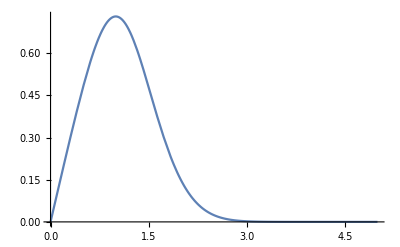

```mathematica
Plot[RPsiMinusSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.s->5/.ds->1/.A->1/.B->1,{r,0,5}]
```

we rewrite it in order to make it easier to use in the numerical code

```mathematica
(A B (Rf[r]+Tf[t,r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (2 ⅇ^(ds^2 (Rf[r]+Tf[t,r])^2) Rf[r]+A B (Rf[r]+ⅇ^(4 ds^2 Rf[r] Tf[t,r]) (Rf[r]-Tf[t,r])+Tf[t,r])))/.Rf[r]-Tf[t,r]->J/.-Rf[r]+Tf[t,r]->-J/.ⅇ^(4 ds^2 Rf[r] Tf[t,r])->K/.(Rf[r]+Tf[t,r])->L
```

(A B (L+K (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))

```mathematica
(A B (L+K (-Tf[t,r]+Rf[r] (-1+2 ds Rf[r]-2 ds Tf[t,r]) (1+2 ds Rf[r]-2 ds Tf[t,r]))) χ[Rf[r]])/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))/. 2 ds Rf[r]-2 ds Tf[t,r]->2dsJ
```

(A B (L+K ((-1+2 dsJ) (1+2 dsJ) Rf[r]-Tf[t,r])) χ[Rf[r]])/(Rf[r] (A B (J K+L)+2 ⅇ^(ds^2 L^2) Rf[r]))

Rescaled PsiPlus initial data for model 1

```mathematica
RRPsiPlusSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))

```mathematica
(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))/.ⅇ^(ds^2 (r-2 Rf[r])^2)->K/.ⅇ^(ds^2 r^2)->J/.ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2))->J*K
```

(A B (-K r+J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]))

We collect the K coefficient, since it could give divergences during the computational implementation

```mathematica
Collect[A B (-K r+J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2,K]
Collect[Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]),K]
```

-A B K r χ[Rf[r]]^2+A B J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r]) χ[Rf[r]]^2

-A B J (r-2 Rf[r]) Rf[r]+K Rf[r] (A B r+2 J Rf[r])

The equation become

```mathematica
(-A B  r χ[Rf[r]]^2+A B J K^-1 (r-4 ds^2 (r-2 Rf[r])^2 Rf[r]) χ[Rf[r]]^2)/(-A B J K^-1 (r-2 Rf[r]) Rf[r]+Rf[r] (A B r+2 J Rf[r]))
```

(-A B r χ[Rf[r]]^2+(A B J (r-4 ds^2 (r-2 Rf[r])^2 Rf[r]) χ[Rf[r]]^2)/K)/(-(A B J (r-2 Rf[r]) Rf[r])/K+Rf[r] (A B r+2 J Rf[r]))

when r ->s:

```mathematica
(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r) χ[Rf[r]]^2)/(2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]^2)//FullSimplify
```

-(A B ⅇ^(-ds^2 r^2) r χ[Rf[r]]^2)/(2 Rf[r]^2)

Hence RRPsiPlus goes to zero when r->s

Then when r->0:

```mathematica
(A B (-ⅇ^(ds^2 (r-2 Rf[r])^2) r+ⅇ^(ds^2 r^2) (r-4 ds^2 (r-2 Rf[r])^2 Rf[r])) χ[Rf[r]]^2)/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))/.r->0
```

-(16 A B ds^2 Rf[0]^2 χ[Rf[0]]^2)/(2 A B Rf[0]+2 ⅇ^(4 ds^2 Rf[0]^2) Rf[0])

RPsiPlus goes to  when r->0

Rescaled PsiMinus initial data for model 1

```mathematica
RPsiMinusSolutionM1[Tf[t,r],Rf[r]]/.TRule/.t->0//FullSimplify
```

(A B (-ⅇ^(ds^2 r^2) (r-2 Rf[r])+ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))

```mathematica
(A B (-ⅇ^(ds^2 r^2) (r-2 Rf[r])+ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(Rf[r] (A B (ⅇ^(ds^2 (r-2 Rf[r])^2) r-ⅇ^(ds^2 r^2) (r-2 Rf[r]))+2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r]))/.ⅇ^(ds^2 (r-2 Rf[r])^2)->K/.ⅇ^(ds^2 r^2)->J/.ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2))->J*K
```

(A B (-J (r-2 Rf[r])+K (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]])/(Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]))

We collect the K coefficients:

```mathematica
Collect[A B (-J (r-2 Rf[r])+K (r+(-2+4 ds^2 r^2) Rf[r])) χ[Rf[r]],K]
Collect[Rf[r] (A B (K r-J (r-2 Rf[r]))+2 J K Rf[r]),K]
```

-A B J (r-2 Rf[r]) χ[Rf[r]]+A B K (r+(-2+4 ds^2 r^2) Rf[r]) χ[Rf[r]]

-A B J (r-2 Rf[r]) Rf[r]+K Rf[r] (A B r+2 J Rf[r])

So we obtain

```mathematica
(-A B J K^-1 (r-2 Rf[r]) χ[Rf[r]]+A B K(r+(-2+4 ds^2 r^2) Rf[r]) χ[Rf[r]])/(-A B J K^-1(r-2 Rf[r]) Rf[r]+ Rf[r] (A B r+2 J Rf[r]))
```

(-(A B J (r-2 Rf[r]) χ[Rf[r]])/K+A B K (r+(-2+4 ds^2 r^2) Rf[r]) χ[Rf[r]])/(-(A B J (r-2 Rf[r]) Rf[r])/K+Rf[r] (A B r+2 J Rf[r]))

In the limit r->s

```mathematica
(A B (ⅇ^(ds^2 (r-2 Rf[r])^2) (r+(-2+4 ds^2 r^2) Rf[r])))/(2 ⅇ^(ds^2 (r^2+(r-2 Rf[r])^2)) Rf[r])//FullSimplify
```

(A B ⅇ^(-ds^2 r^2) (r+(-2+4 ds^2 r^2) Rf[r]))/(2 Rf[r])